0.1

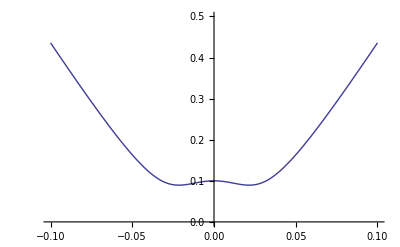

```mathematica
d=0.12; t=0.4; c=6.25;a1=0.00125; G1=0.00086; b=0.0004138; mu1=0.13;
f4[x_,n1_,U_]:=√(U^2+(a1*n1/x)+t^2/2-√((t^2+4*U^2)*(a1*n1/x)+t^4/4));
f4[0.1,1,0.1];
F2[x_,n1_,U_]=(1/((mu1-f4[x,n1,U])^2+G1^2));
F1[x_,U_]=b*G1*Sum[F2[x,n1,U],{n1,0,100}]*(1/x);
f144[x_,U_]:=√(U^2+(6.25*x)^2+t^2*0.5-√((t^2+4*U^2)*(6.25*x)^2+t^4/4));
f144[0,0.1]
Plot[f144[x,0.1],{x,-0.1,0.1},PlotRange->{0,0.5}]
DiscretePlot[f4[1,n1,0.1],{n1,0,10},PlotMarkers->{"•",Large},PlotStyle->{Red},Frame->True ];
```

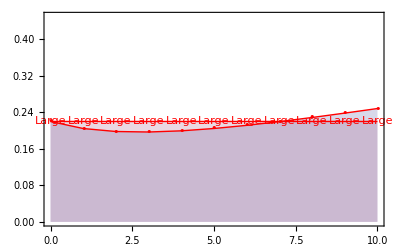

```mathematica
f5[x_,n1_,U_]:=√(d^2+U^2+(a1*n1*x)+t^2/2-√((t^2+4*U^2)*(a1*n1*x)+4*U^2*d^2+2*t^2*d*U+t^4/4));
f55[x_,U_]:=√(d^2+U^2+(6.25*x)^2+t^2/2-√((t^2+4*U^2)*(6.25*x)^2+4*U^2*d^2+2*t^2*d*U+t^4/4));

DiscretePlot[{f5[10,n1,-0.1],0.22},{n1,0,10},PlotRange->{0,0.45},PlotMarkers->{"•",Large},PlotStyle->{Red},Joined->True,Frame->True]
```

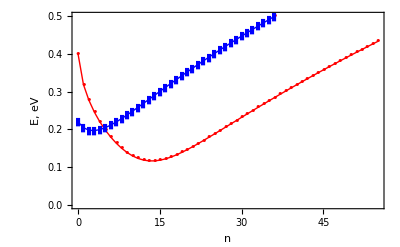

```mathematica
d=0.12; mu3=0.13;
f6[x_,n1_,U_]:=√(d^2+U^2+(a1*n1*x)+t^2-2*√((t^2+U^2)*(a1*n1*x)+U^2*d^2))
DiscretePlot[{f6[10,n1,-0.1],f5[10,n1,-0.1]},{n1,0,55},PlotRange->{0,0.5},PlotMarkers->{{"•"},{"▮"}},PlotStyle->{Red,Blue},Joined->True,FrameLabel->{Style["n",10],Style["E, eV",10]},Filling->None,Frame->True]
```